```mathematica
Clear["Global`*"];
(*Needs["MathPDE`"];*)
Needs["NDSolve`FEM`"];
P           = 20.;                      (* Laser Power [W] *)
nIndex = 1.6;                    (* Refraction index [dimensionless] *)
P           = P  (nIndex^2+1)/(2nIndex);(* Recalculation of Laser Power inside the crystal [W] *)
h           = 31;                       (* Heat Exchange Coefficient [W/m^2/K]*)
k           = 5.2 ;                   (* Thermal Conductivity [W/m/K] *)
c           = 1022;                  (* Thermal Сapacity [J/kg/K] *)
ρ       = 2470;                      (* Density [kg/m^3] *)
lx         = 42. 10^-3;          (* X-size [m] *)
ly         = 5. 10^-3;            (* Y-size [m] *)
lz         = 5. 10^-3;            (* Z-size [m] *)
β           =5.6 10^-3;        (* Volume Absorption Coefficient [1/m] *)
S            = 14. 10^-3;        (* Surface Absorption Coefficient [1/m] *)
t1          = 100.;                    (* Heating Stop Time [s] *)
α            =  k/c/ρ;         (* [m^2/s] *)
μ = 5. 10^-4;
TempBound = 0;
(*g[x_,y_, z_, t_] = Piecewise[{
{P*(β + S(DiracDelta[x] + DiracDelta[lx-x]))* DiracDelta[y] *DiracDelta[z], 0<t< t1 },
{0, t>t1 }
}];*)
(*g[x_,y_, z_] = P*(β + S(DiracDelta[x] + DiracDelta[lx-x]))* DiracDelta[ly/2-y] *DiracDelta[lz/2-z]*)
g[x_,y_, z_] = P 1/(2π μ^2)(β + S/(√(2π)μ)(Exp[-(x)^2/(2 μ^2)] + Exp[-(x-lx)^2/(2 μ^2)]))* Exp[-((y-ly/2)^2+(z-lz/2)^2)/(2 μ^2)]
```

1.41648×10^7 ⅇ^(-2.×10^6 ((-0.0025+y)^2+(-0.0025+z)^2)) (0.0056+11.1704 (ⅇ^(-2.×10^6 (-0.042+x)^2)+ⅇ^(-2.×10^6 x^2)))

```mathematica
region = Cuboid[{0,0,0},{lx, ly, lz}];
```

```mathematica
(*NDSolveValue[{∇_{x,y, z}^2 u[t, x,y,z]- 1/α D[u[t, x,y,z], t]+1/k g[x, y, z]== NeumannValue[h*(-u[t, x,y,z]+TempBound), True], u[0,x,y,z] == 0},u, {t, 0, t1}, {x,y,z}∈region]*)
NDSolveValue[{-k*∇_{x,y, z}^2 u[t, x,y,z]+ k/α D[u[t, x,y,z], t]- g[x, y, z]== NeumannValue[h*(-u[t, x,y,z]+TempBound), True], u[0,x,y,z] == 0},u, {t, 0, t1}, {x,y,z}∈region]
```

InterpolatingFunction[{{0., 100.}, {0., 0.042}, {0., 0.005}, {0., 0.005}}, <>]

```mathematica
solution[t_, x_, y_, z_] = %[t,x,y,z];
```

Manipulation with results

```mathematica
solution[49,lx, ly/2, lz/2]
(*ContourPlot[%[t,x,ly/2+0.001,lz/2+0.001],{x, 0, lx}, {t, 0, t1}]*)
```

15.2208

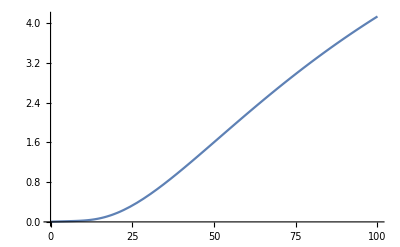

```mathematica
Plot[solution[t,lx/2, ly/2, lz/2], {t, 0, t1}]
```

```mathematica
Manipulate[Plot3D[solution[t,x, y,lz/2],{x, 0, lx},{y, 0, ly}, PlotLegends->Automatic, PlotRange->Full, Mesh->All], {t, 0, 40.}]
```